```mathematica
dataA=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/361/A.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataA//TableForm
```

```mathematica
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
forTeXA=MapAt[dropLastDot@*ToString,dataA,{{2;;,All}}];
forTeXA//TeXForm
```

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
myTicksX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.2}]
myTicksY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.2}]
```

FittedModel[-1.49023+1.02951 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.49023 | 0.264366 | -5.637 | 0.00133475
x | 1.02951 | 0.0172515 | 59.6766 | 1.48785×10^-9

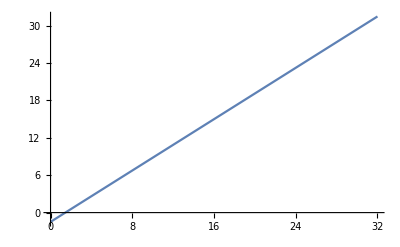

```mathematica
forFitA=dataA⟦2;;,{4,3}⟧;
fitA=LinearModelFit[forFitA,{1,x},x]
fitA@"ParameterTable"
Plot[fitA["Function"]@x, {x, 0, 32}]
```

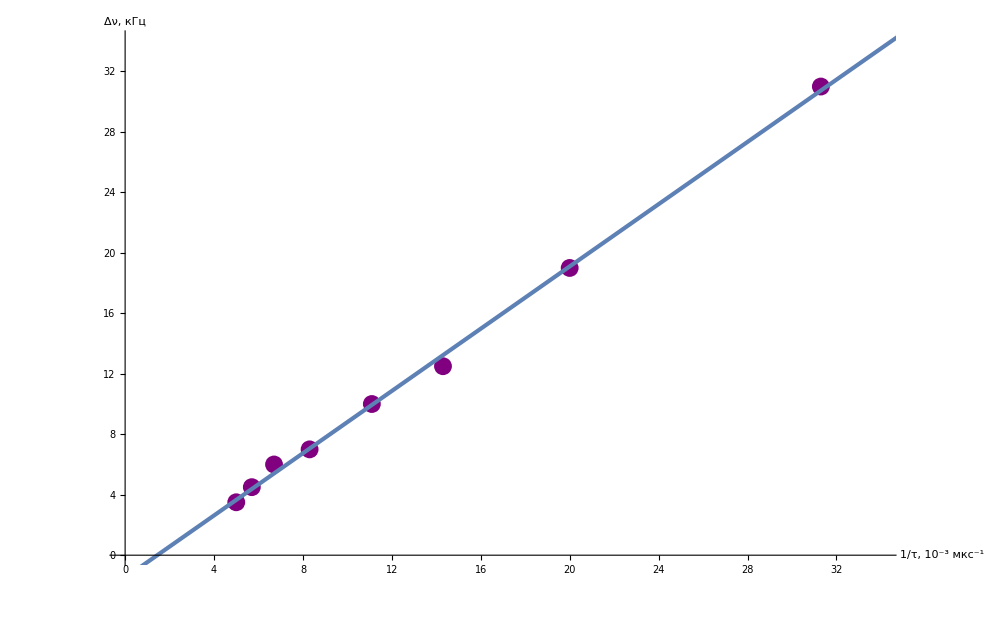

```mathematica
Show[ListPlot[dataA⟦2;;,{4,3}⟧,
GridLines->{grids@2.5,grids@2.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"1/τ, 10^-3 (:043c:043a:0441)^-1","Δν, кГц"},
AxesStyle->Directive[Large,Black],
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,34},{0,34}},
ImageSize->1000], Plot[fitA["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

```mathematica
dataB=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/361/B.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataB//TableForm
```

```mathematica
forTeXB=MapAt[dropLastDot@*ToString,dataB,{{2;;,All}}];
forTeXB//TeXForm
```

```mathematica
forFitB=dataB⟦2;;,{2,3}⟧;
fitB=LinearModelFit[forFitB,{1,x},x]
fitB@"ParameterTable"
Plot[fitB["Function"]@x, {x, 0, 9.9}]
```

```mathematica
Show[ListPlot[dataB⟦2;;,{2,3}⟧,
GridLines->{grids@1,grids@1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"f_(:043f:043e:0432:0442), кГц","δν, кГц"},
AxesStyle->Directive[Large,Black],
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,9.9},{0,9.9}},
ImageSize->1000], Plot[fitB["Function"]@x,{x,0,10}, PlotStyle->Thickness@0.003]]
```

```mathematica
dataC=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/361/C.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataC//TableForm
```

N | Amin | Amax | Aосн | Aбок | m | А/A
1. | 1. | 1.8 | 6. | 1.1 | 0.29 | 0.18
2. | 0.6 | 2. | 6.3 | 2. | 0.54 | 0.32
3. | 0.4 | 2.3 | 6.5 | 2.7 | 0.7 | 0.42
4. | 0.2 | 2.5 | 6.3 | 3.2 | 0.85 | 0.51
5. | 0.8 | 1.8 | 6.3 | 1.5 | 0.38 | 0.24

```mathematica
forTeXC=MapAt[dropLastDot@*ToString,dataC,{{2;;,All}}];
forTeXC//TeXForm
```

\left(
\begin{array}{ccccccc}
 \text{N} & \text{Amin} & \text{Amax} & \text{A$\unicode{043e}\unicode{0441}\unicode{043d}$} & \text{A$\unicode{0431}\unicode{043e}\unicode{043a}$} & \text{m}
   & \text{$\unicode{0410}$/A} \\
 1 & 1 & 1.8 & 6 & 1.1 & 0.29 & 0.18 \\
 2 & 0.6 & 2 & 6.3 & 2 & 0.54 & 0.32 \\
 3 & 0.4 & 2.3 & 6.5 & 2.7 & 0.7 & 0.42 \\
 4 & 0.2 & 2.5 & 6.3 & 3.2 & 0.85 & 0.51 \\
 5 & 0.8 & 1.8 & 6.3 & 1.5 & 0.38 & 0.24 \\
\end{array}
\right)

FittedModel[0.0122728+0.582839 x]

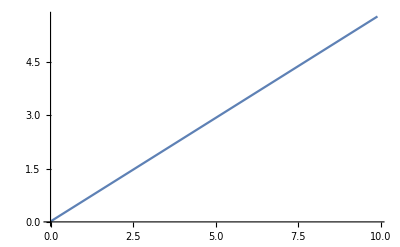

\begin{array}{l|llll}
 \text{} & \text{Estimate} & \text{Standard Error} & \text{t-Statistic} & \text{P-Value} \\
\hline
 1 & 0.0122728 & 0.00725315 & 1.69207 & 0.18921 \\
 x & 0.582839 & 0.0123215 & 47.3027 & 0.0000208024 \\
\end{array}

```mathematica
forFitC=dataC⟦2;;,{6,7}⟧;
fitC=LinearModelFit[forFitC,{1,x},x]
fitC@"ParameterTable"//TeXForm
Plot[fitC["Function"]@x, {x, 0, 9.9}]
```

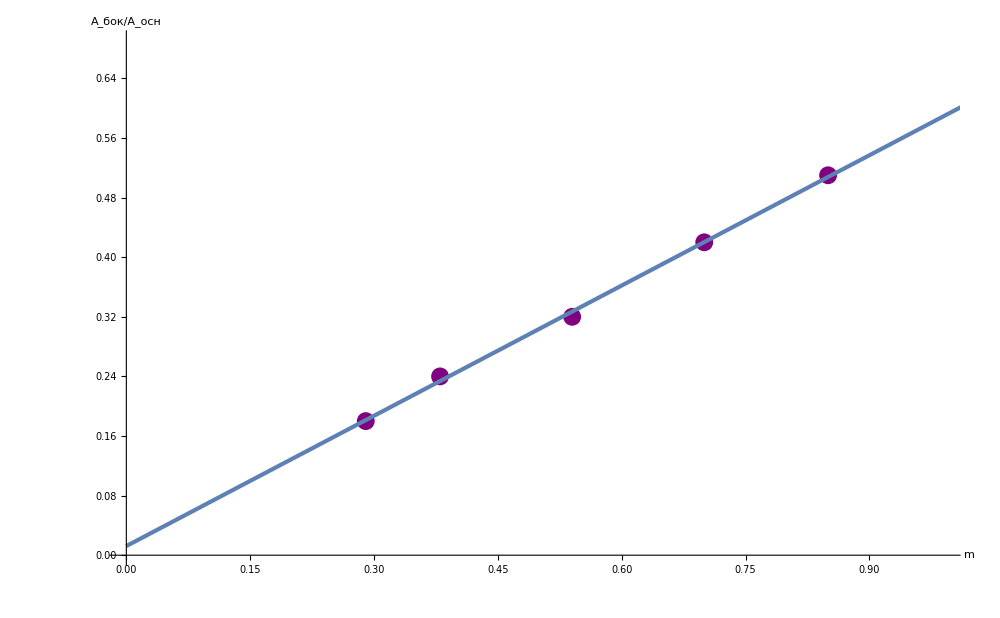

```mathematica
Show[ListPlot[dataC⟦2;;,{6,7}⟧,
GridLines->{grids@0.1,grids@0.1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"m","(A_(:0431:043e:043a))/((:0410)_(:043e:0441:043d))"},
AxesStyle->Directive[Large,Black],
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,0.99},{0,0.69}},
ImageSize->1000], Plot[fitC["Function"]@x,{x,0,10}, PlotStyle->Thickness@0.003]]
```

```mathematica
dataU=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/334/U.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
```

```mathematica
forTeXU=MapAt[dropLastDot@*ToString,dataU,{{2;;,All}}];
forTeXU//TeXForm
```

```mathematica
dataE=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/334/E.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
```

```mathematica
forTeXE=MapAt[dropLastDot@*ToString,dataE,{{2;;,All}}];
forTeXE//TeXForm
```

StringTake::take: Cannot take positions -1 through -1 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

\left(
\begin{array}{cccccccccc}
 \text{N} & \text{Im, A} & 0.22 & 0.35 & 0.5 & 0.6 & 0.7 & 0.85 & 1.07 & 1.07 \\
 \text{} & \text{} & \text{U} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 1 & 0.1 & -8 & -10 & -14 & -16 & -20 & -25 & -29 & -28 \\
 2 & 0.3 & -19 & -31 & -45 & -54 & -62 & -75 & -96 & -94 \\
 3 & 0.6 & -38 & -62 & -89 & -106 & -127 & -152 & -188 & -192 \\
 4 & 0.9 & -55 & -87 & -122 & -151 & -173 & -209 & -262 & -277 \\
 5 & 1.2 & -68 & -106 & -151 & -183 & -213 & -256 & -324 & -342 \\
 6 & 1.5 & -76 & -120 & -169 & -205 & -239 & -289 & -364 & -389 \\
 7 & 1.8 & -82 & -128 & -191 & -219 & -257 & -310 & -389 & -418 \\
 8 & 2.1 & -86 & -134 & -190 & -229 & -268 & -321 & -404 & -434 \\
\end{array}
\right)

```mathematica
dataR=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/334/R.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
```

```mathematica
forTeXR=MapAt[dropLastDot@*ToString,dataR,{{2;;,All}}];
forTeXR//TeXForm
```

StringTake::take: Cannot take positions -1 through -1 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

\left(
\begin{array}{cccccccccc}
 \text{N} & \text{B} & 0.22 & 0.35 & 0.5 & 0.6 & 0.7 & 0.85 & 1.07 & 1.07 \\
 \text{} & \text{} & \text{U} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 1 & 0.17 & 4.7 & 3.7 & 3.6 & 3.5 & 3.7 & 3.8 & 3.5 & 3.4 \\
 2 & 0.19 & 10 & 10.3 & 10.4 & 10.4 & 10.3 & 10.2 & 10.4 & 10.2 \\
 3 & 0.37 & 10.3 & 10.5 & 10.6 & 10.5 & 10.8 & 10.6 & 10.4 & 10.7 \\
 4 & 0.53 & 10.4 & 10.3 & 10.1 & 10.4 & 10.3 & 10.2 & 10.2 & 10.7 \\
 5 & 0.69 & 9.9 & 9.7 & 9.6 & 9.7 & 9.7 & 9.6 & 9.7 & 10.2 \\
 6 & 0.8 & 9.5 & 9.4 & 9.3 & 9.4 & 9.4 & 9.4 & 9.4 & 10 \\
 7 & 0.86 & 9.5 & 9.4 & 9.8 & 9.3 & 9.4 & 9.3 & 9.3 & 10 \\
 8 & 0.92 & 9.3 & 9.2 & 9.1 & 9.1 & 9.2 & 9 & 9 & 9.7 \\
\end{array}
\right)